```mathematica
diamonds=Import[$HomeDirectory<>"/Rtmp/diamonds.csv"];

(*Replacec empty string with index*)
diamonds[[1,1]] = "index"; 

(*Convert to DataSet*)
dSet=Dataset@Table[
Association@(Rule@@#&/@Thread[{diamonds[[1]],diamond}]),
{diamond,diamonds[[2;;-1]]}
];
```

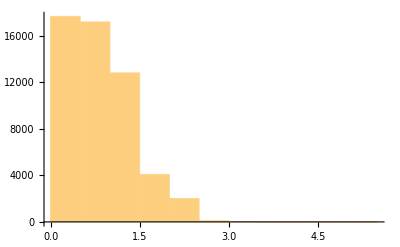

```mathematica
dSet[Histogram[#,{.5}]&,"carat"]
```

```mathematica
Histogram[dSet[All,"carat"],{.5}]
```

-Graphics-

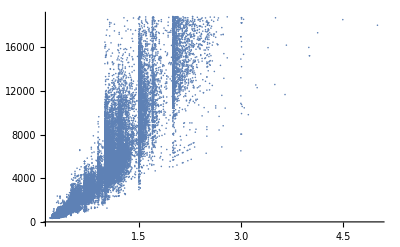

```mathematica
dSet[ListPlot[#,PlotRange->Full]&,{"carat","price"}]
```

```mathematica
ListPlot[dSet[All,{"carat","price"}],PlotRange->Full]
```

-Graphics-

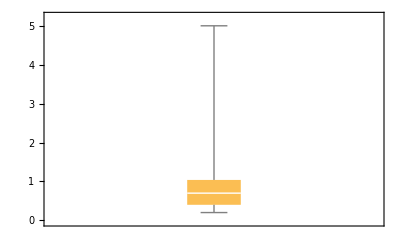

```mathematica
dSet[BoxWhiskerChart,"carat"]
```

```mathematica
BoxWhiskerChart[dSet[All,"carat"]]
```

-Graphics-

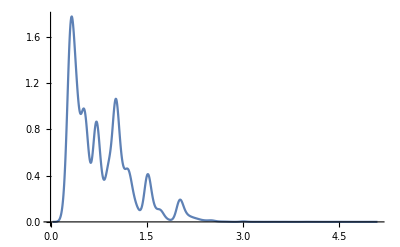

```mathematica
dSet[SmoothHistogram[#,PlotRange->Full]&,"carat"]
```

```mathematica
SmoothHistogram[dSet[All,"carat"],PlotRange->Full]
```

-Graphics-

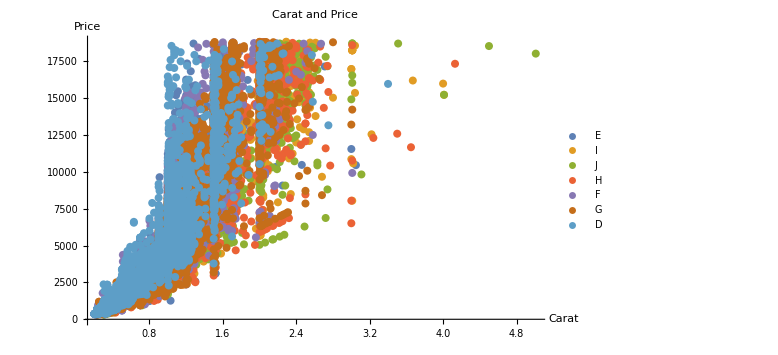

```mathematica
ListPlot[
dSet[GroupBy["color"],All,{"carat","price"}],
PlotRange->Full,
PlotLabel->"Carat and Price",
AxesLabel->{"Carat","Price"},
PlotStyle->{PointSize[.01]},
PlotLegends->Placed[DeleteDuplicates@Normal@dSet[All,"color"],Above],
ImageSize->Large]
```

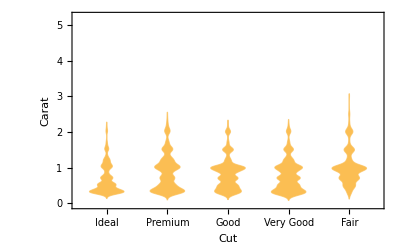

```mathematica
DistributionChart[
Values@Normal@dSet[GroupBy["cut"],All,"carat"],
FrameLabel->{"Cut","Carat"},
ChartLabels->Normal@DeleteDuplicates@dSet[All,"cut"]
]
```